# Mean-field solution

## Evaluate notebook

```mathematica
Needs["MaTeX`"]
```

### Plots

#### Loading the data from files ...

```mathematica
fN =FileNameJoin[{NotebookDirectory[],"l_25.txt"}];
f = OpenRead[fN];
cb25 = ReadList[ f];
Close[f];
```

```mathematica
c25 = Legended[Table[ {cb25⟦i,1⟧,cb25⟦i,2⟧} ,{i,1,Length[cb25]}],   MaTeX["\\ell = 25",Magnification->1.4] ];
b25= Legended[Table[ {cb25⟦i,1⟧,cb25⟦i,3⟧} ,{i,1,Length[cb25]}],   MaTeX["\\ell = 25",Magnification->1.4] ];
```

```mathematica
fN =FileNameJoin[{NotebookDirectory[],"l_50.txt"}];
f = OpenRead[fN];
cb50 = ReadList[ f];
Close[f];
```

```mathematica
c50 = Legended[Table[ {cb50⟦i,1⟧,cb50⟦i,2⟧} ,{i,1,Length[cb50]}],   MaTeX["\\ell = 50",Magnification->1.4] ];
b50= Legended[Table[ {cb50⟦i,1⟧,cb50⟦i,3⟧} ,{i,1,Length[cb50]}],   MaTeX["\\ell = 50",Magnification->1.4] ];
```

```mathematica
fN = FileNameJoin[{NotebookDirectory[],"l_100.txt"}];
f = OpenRead[fN];
cb100 = ReadList[ f];
Close[f];
```

```mathematica
c100 = Legended[Table[ {cb100⟦i,1⟧,cb100⟦i,2⟧} ,{i,1,Length[cb100]}],   MaTeX["\\ell = 100",Magnification->1.4] ];
b100= Legended[Table[ {cb100⟦i,1⟧,cb100⟦i,3⟧} ,{i,1,Length[cb100]}],   MaTeX["\\ell = 100",Magnification->1.4] ];
```

```mathematica
fN = FileNameJoin[{NotebookDirectory[],"l_150.txt"}];
f = OpenRead[fN];
cb150 = ReadList[ f];
Close[f];
```

```mathematica
c150 = Legended[Table[ {cb150⟦i,1⟧,cb150⟦i,2⟧} ,{i,1,Length[cb150]}],   MaTeX["\\ell = 150",Magnification->1.4] ];
b150= Legended[Table[ {cb150⟦i,1⟧,cb150⟦i,3⟧} ,{i,1,Length[cb150]}],   MaTeX["\\ell = 150",Magnification->1.4] ];
```

```mathematica
fN = FileNameJoin[{NotebookDirectory[],"l_250.txt"}];
f = OpenRead[fN];
cb250 = ReadList[ f];
Close[f];
```

```mathematica
c250 = Legended[Table[ {cb250⟦i,1⟧,cb250⟦i,2⟧} ,{i,1,Length[cb250]}],   MaTeX["\\ell = 250",Magnification->1.4] ];
b250= Legended[Table[ {cb250⟦i,1⟧,cb250⟦i,3⟧} ,{i,1,Length[cb250]}],   MaTeX["\\ell = 250",Magnification->1.4] ];
```

```mathematica
fN = FileNameJoin[{NotebookDirectory[],"l_350.txt"}];
f = OpenRead[fN];
cb350 = ReadList[ f];
Close[f];
```

```mathematica
c350 = Legended[Table[ {cb350⟦i,1⟧,cb350⟦i,2⟧} ,{i,1,Length[cb350]}],   MaTeX["\\ell = 350",Magnification->1.4] ];
b350= Legended[Table[ {cb350⟦i,1⟧,cb350⟦i,3⟧} ,{i,1,Length[cb350]}],   MaTeX["\\ell = 350",Magnification->1.4] ];
```

#### Mean-field parameters versus different lattice sizes

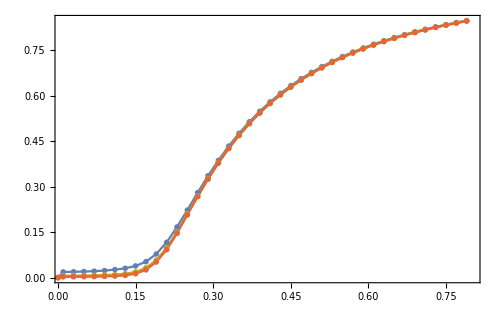

```mathematica
t =ListPlot[ {b50,b150,b250,b350}, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {{.01,.8},All},Joined->True, PlotMarkers->"OpenMarkers",Frame->True,(*PlotStyle->{Darker[Blue]}, *)  FrameStyle->Directive[Thickness[.002],Black,14],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ]
```

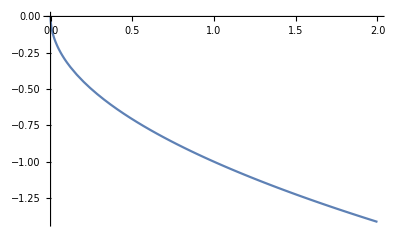

```mathematica
Plot[ -Sqrt[x],{x,0,2}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chib.pdf"}],t];
```

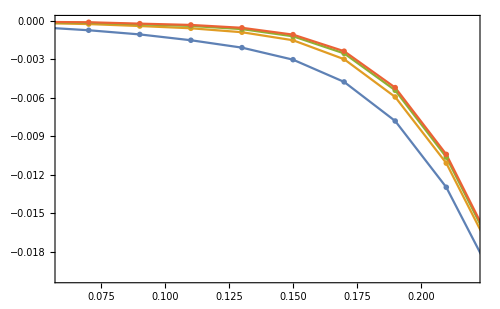

```mathematica
t=ListPlot[ {c50,c150,c250,c350}, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] } , PlotRange->{{.06,.22},{0,-.02}},Joined->True, PlotMarkers->"OpenMarkers",Frame->True,(*PlotStyle->{Darker[Blue]}, *)  FrameStyle->Directive[Thickness[.002],Black,14],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chic.pdf"}],t];
```

#### Size dependence for fixed J̃ = 0.09

```mathematica
index = 6;
title = StringReplace["\\chi_c(\\tilde{J}=X)", "X"-> TextString[c50⟦1⟧⟦index,1⟧]];
clInv=ListPlot[ Legended[{{ 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False,  PlotMarkers->{"OpenMarkers"},Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotStyle->{Darker[Red]} ] ;
```

```mathematica
clInfFit = Fit[cL, {1,x},x];
```

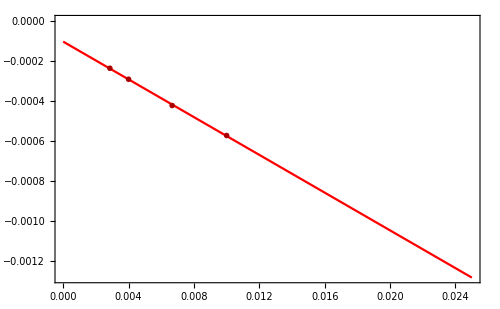

```mathematica
t=Show[ Plot[ Legended[clInfFit, MaTeX[StringReplace[ToString[SetAccuracy[clInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Red},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], clInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chic-J-9-100.pdf"}],t];
```

```mathematica
index = 6;
title = StringReplace["\\chi_b(\\tilde{J}=X)", "X"-> TextString[b50⟦1⟧⟦index,1⟧]];
blInv=ListPlot[ Legended[{ { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }} , MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False, PlotMarkers->{"OpenMarkers"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ] ;
```

```mathematica
blInfFit = Fit[{ { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

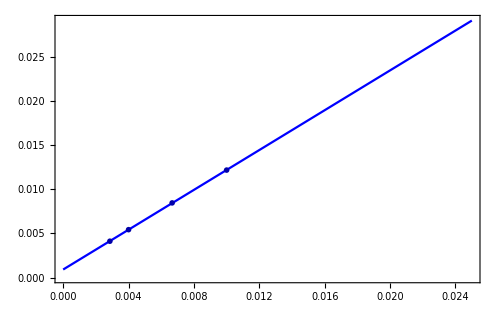

```mathematica
t=Show[ Plot[ Legended[blInfFit,  MaTeX[StringReplace[ToString[SetAccuracy[blInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Blue},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], blInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chib-J-9-100.pdf"}],t];
```

#### Size dependence for fixed J̃ = 0.07

```mathematica
index = 5;
title = StringReplace["\\chi_c(\\tilde{J}=X)", "X"-> TextString[c50⟦1⟧⟦index,1⟧]];
clInv=ListPlot[ Legended[{{ 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False,  PlotMarkers->{"OpenMarkers"},Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotStyle->{Darker[Red]} ] ;
```

```mathematica
clInfFit = Fit[{ { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

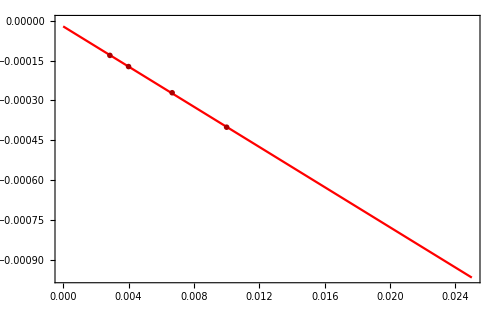

```mathematica
t=Show[ Plot[ Legended[clInfFit, MaTeX[StringReplace[ToString[SetAccuracy[clInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Red},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], clInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chic-J-7-100.pdf"}],t];
```

```mathematica
index = 5;
title = StringReplace["\\chi_b(\\tilde{J}=X)", "X"-> TextString[b50⟦1⟧⟦index,1⟧]];
blInv=ListPlot[ Legended[{ { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False, PlotMarkers->{"OpenMarkers"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ] ;
```

```mathematica
blInfFit = Fit[{ { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

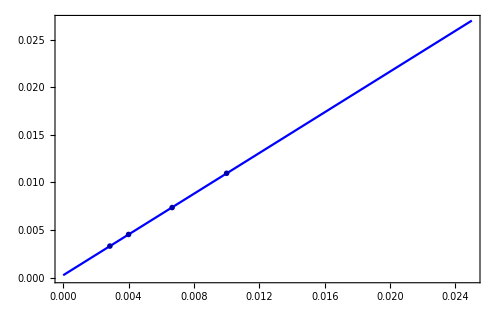

```mathematica
t=Show[ Plot[ Legended[blInfFit,  MaTeX[StringReplace[ToString[SetAccuracy[blInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Blue},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], blInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chib-J-7-100.pdf"}],t];
```

#### Size dependence for fixed J̃ = 0.11

```mathematica
index = 7;
title = StringReplace["\\chi_c(\\tilde{J}=X)", "X"-> TextString[c50⟦1⟧⟦index,1⟧]];
clInv=ListPlot[ Legended[{ { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False,  PlotMarkers->{"OpenMarkers"},Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotStyle->{Darker[Red]} ] ;
```

```mathematica
clInfFit = Fit[{ { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

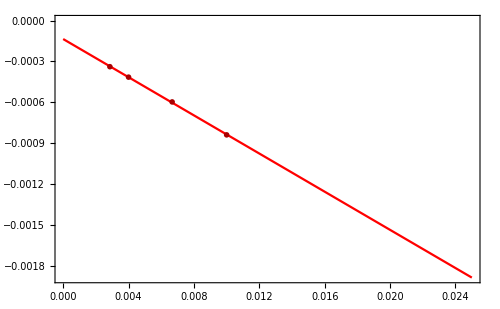

```mathematica
t=Show[ Plot[ Legended[clInfFit, MaTeX[StringReplace[ToString[SetAccuracy[clInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Red},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], clInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chic-J-11-100.pdf"}],t];
```

```mathematica
index = 7;
title = StringReplace["\\chi_b(\\tilde{J}=X)", "X"-> TextString[b50⟦1⟧⟦index,1⟧]];
blInv=ListPlot[ Legended[{{ 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False, PlotMarkers->{"OpenMarkers"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ] ;
```

```mathematica
data = {{ 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }}
```

{{1/100,0.0109573},{1/150,0.00735581},{1/250,0.00453119},{1/350,0.00331021}}

```mathematica
blInfFit = Fit[{ { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

```mathematica
fit[x_] := 0.0002465865434949214+1.0699024710110219 x
```

```mathematica
tab = Table[ ( data[[i,2]] -fit[data[[i,1]] ])^2,{i,1,4}]
```

{1.37211×10^-10,5.50366×10^-10,2.48902×10^-11,4.56594×10^-11}

```mathematica
Sqrt[Sum[tab[[i]] , {i,1,4}]]/2 //ScientificForm
```

1.3767×10^-5

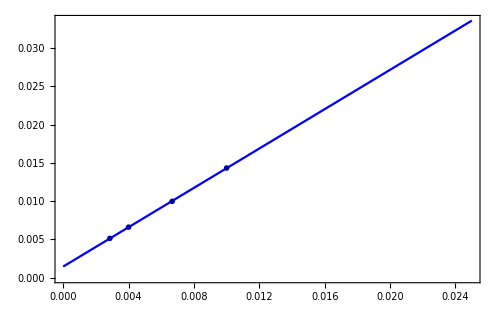

```mathematica
t=Show[ Plot[ Legended[blInfFit,  MaTeX[StringReplace[ToString[SetAccuracy[blInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Blue},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], blInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chib-J-11-100.pdf"}],t];
```

#### Size dependence for a fixed J̃ = 0.13

```mathematica
index = 8;
title = StringReplace["\\chi_c(\\tilde{J}=X)", "X"-> TextString[c50⟦1⟧⟦index,1⟧]];
clInv=ListPlot[ Legended[{{50^-1,c50⟦1⟧⟦index,2⟧ }, { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False,  PlotMarkers->{"OpenMarkers"},Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotStyle->{Darker[Red]} ] ;
```

```mathematica
clInfFit = Fit[{{50^-1,c50⟦1⟧⟦index,2⟧ }, { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

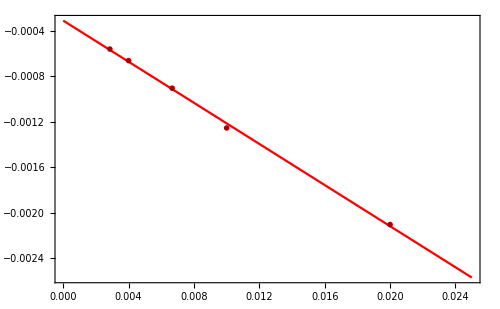

```mathematica
t=Show[ Plot[ Legended[clInfFit, MaTeX[StringReplace[ToString[SetAccuracy[clInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Red},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], clInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chic-J-13.pdf"}],t];
```

```mathematica
index = 8;
title = StringReplace["\\chi_b(\\tilde{J}=X)", "X"-> TextString[b50⟦1⟧⟦index,1⟧]];
blInv=ListPlot[ Legended[{{50^-1,b50⟦1⟧⟦index,2⟧ }, { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False, PlotMarkers->{"OpenMarkers"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ] ;
```

```mathematica
blInfFit = Fit[{{50^-1,b50⟦1⟧⟦index,2⟧ }, { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

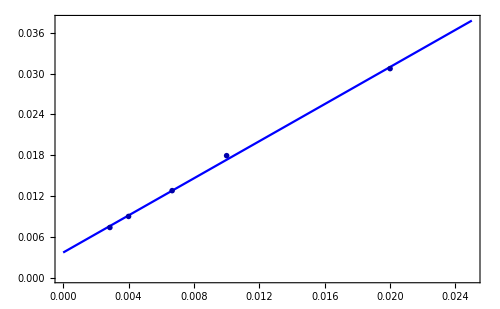

```mathematica
t=Show[ Plot[ Legended[blInfFit,  MaTeX[StringReplace[ToString[SetAccuracy[blInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Blue},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], blInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chib-J-13.pdf"}],t];
```

#### Size dependence for a fixed J̃ = 0.15

```mathematica
index = 9;
title = StringReplace["\\chi_c(\\tilde{J}=X)", "X"-> TextString[c50⟦1⟧⟦index,1⟧]];
clInv=ListPlot[ Legended[{ { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False,  PlotMarkers->{"OpenMarkers"},Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotStyle->{Darker[Red]} ] ;
```

```mathematica
clInfFit = Fit[{ { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

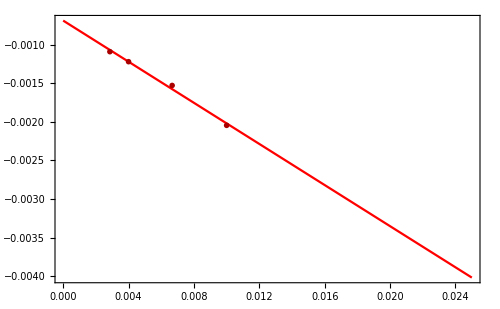

```mathematica
t=Show[ Plot[ Legended[clInfFit, MaTeX[StringReplace[ToString[SetAccuracy[clInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Red},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], clInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chic-J-15-100.pdf"}],t];
```

```mathematica
index = 9;
title = StringReplace["\\chi_b(\\tilde{J}=X)", "X"-> TextString[b50⟦1⟧⟦index,1⟧]];
blInv=ListPlot[ Legended[{{ 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False, PlotMarkers->{"OpenMarkers"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ] ;
```

```mathematica
blInfFit = Fit[{{ 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

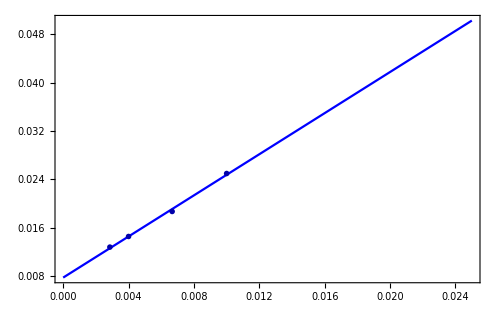

```mathematica
t=Show[ Plot[ Legended[blInfFit,  MaTeX[StringReplace[ToString[SetAccuracy[blInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Blue},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], blInv ]
```

```mathematica
Fit[{{ 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }} , {1,x},x]
```

0.00776873+1.69954 x

```mathematica
fit[x_] :=0.007768734253469516+1.6995395930084225 x
```

```mathematica
data = {{ 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }}
```

{{1/100,0.0249766},{1/150,0.0187007},{1/250,0.0145668},{1/350,0.0128106}}

```mathematica
tab = Table[ ( data[[i,2]] -fit[data[[i,1]] ])^2,{i,1,4}]
```

{4.51446×10^-8,1.5868×10^-7,1.7309×10^-14,3.45981×10^-8}

```mathematica
Sqrt[Sum[tab[[i]] , {i,1,4}]]/2 //ScientificForm
```

2.44143×10^-4

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chib-J-15-100.pdf"}],t];
```

#### Size dependence for a fixed J̃ = 0.17

```mathematica
index = 10;
title = StringReplace["\\chi_c(\\tilde{J}=X)", "X"-> TextString[c50⟦1⟧⟦index,1⟧]];
clInv=ListPlot[ Legended[{ { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False,  PlotMarkers->{"OpenMarkers"},Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotStyle->{Darker[Red]} ] ;
```

```mathematica
clInfFit = Fit[{ { 100^-1 ,c100⟦1⟧⟦index,2⟧},{ 150^-1,c150⟦1⟧⟦index,2⟧ },{ 250^-1,c250⟦1⟧⟦index,2⟧ },{ 350^-1,c350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

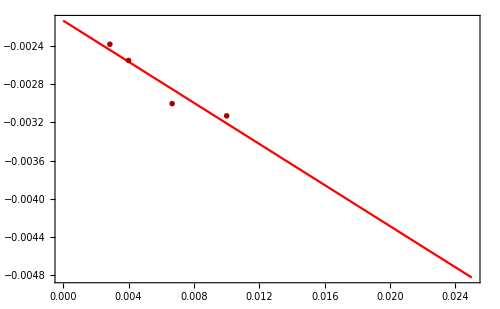

```mathematica
t=Show[ Plot[ Legended[clInfFit, MaTeX[StringReplace[ToString[SetAccuracy[clInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Red},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], clInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chic-J-17-100.pdf"}],t];
```

```mathematica
index = 10;
title = StringReplace["\\chi_b(\\tilde{J}=X)", "X"-> TextString[b50⟦1⟧⟦index,1⟧]];
blInv=ListPlot[ Legended[{ { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }}, MaTeX["\\text{data}",Magnification->1.3]], FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } , PlotRange->All,Joined->False, PlotMarkers->{"OpenMarkers"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ] ;
```

```mathematica
blInfFit = Fit[{ { 100^-1 ,b100⟦1⟧⟦index,2⟧},{ 150^-1,b150⟦1⟧⟦index,2⟧ },{ 250^-1,b250⟦1⟧⟦index,2⟧ },{ 350^-1,b350⟦1⟧⟦index,2⟧ }} , {1,x},x];
```

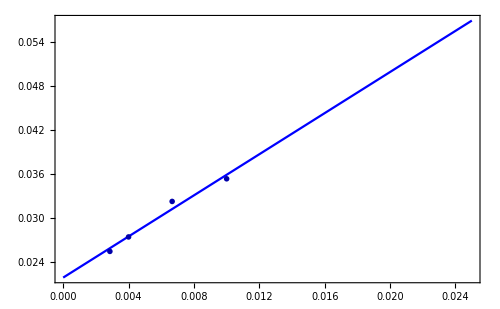

```mathematica
t=Show[ Plot[ Legended[blInfFit,  MaTeX[StringReplace[ToString[SetAccuracy[blInfFit ,6] ] , "x" -> "\\, \\ell^{-1}"],Magnification->1.3]],{x,0,0.025} , PlotStyle->{Blue},FrameLabel-> { MaTeX["\\ell^{-1}",Magnification->2] ,  MaTeX[title,Magnification->1.6] } ,Frame->True,  FrameStyle->Directive[Thickness[.0023],Black,12],ImageSize->500 ], blInv ]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"chib-J-17-100.pdf"}],t];
```